```mathematica
data1=Import["/home/jayz/Dokumente/Studium/Master/WARB/HiggsScan/scripted/result_taurus_1"];data2=Import["/home/jayz/Dokumente/Studium/Master/WARB/HiggsScan/scripted/result_taurus_2"];data3=Import["/home/jayz/Dokumente/Studium/Master/WARB/HiggsScan/scripted/result_taurus_3"];
```

```mathematica
cleanData1=Cases[Drop[#,{3}]&/@data1,Except[{_,_,0}]];cleanData2=Cases[Drop[#,{3}]&/@data2,Except[{_,_,0}]];cleanData3=Cases[Drop[#,{3}]&/@data3,Except[{_,_,0}]];
```

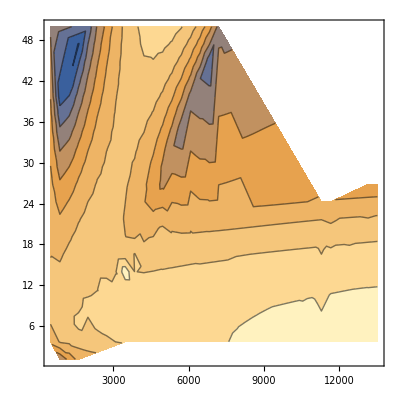

```mathematica
ListContourPlot[cleanData1]
```

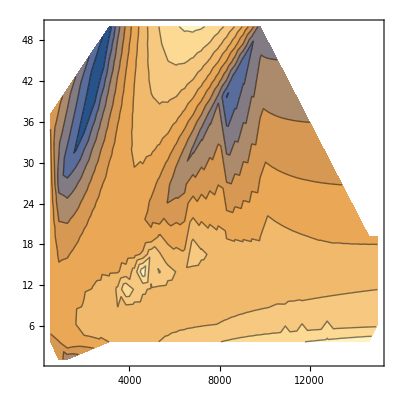

```mathematica
ListContourPlot[cleanData2]
```

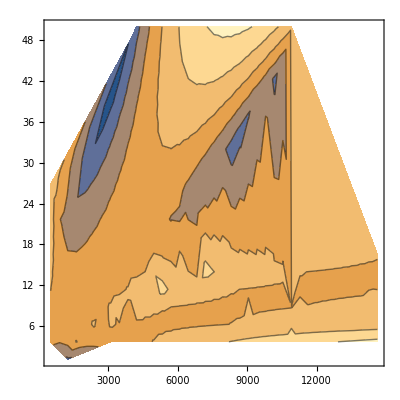

```mathematica
ListContourPlot[cleanData3]
```